## 2 | Variational Quantum Eigensolver (VQE)

The variational quantum eigensolver (VQE) is a hybrid algorithm that combines classical and quantum computing to determine the ground state energy of a Hamiltonian. It utilizes quantum algorithms to calculate expected energy values and classical optimization techniques for minimizing that energy.

VQE plays a crucial role in quantum optimization, particularly in solving complex problems in quantum chemistry and materials science. By enabling efficient simulations of intricate systems, VQE can address optimization tasks that are challenging for classical methods alone.

Given a Hamiltonian operator H, this method consist of two main components:

1. A  variational circuit ansatz V(θ,,).

2. A cost function ℒ=ϕ(θ)Hϕ(θ), where ϕ (θ)=V(θ,,)0

The method  involves iteratively adjusting θ to minimize the average energy or cost function 𝒻.

### Implementation

In order to understand how to proceed with the VQE algorithm, let's drive  a variational state ϕ(θ) to the ground state of the following Hamiltonian:

```mathematica
H=QuantumOperator["X"+"Z"]
```

QuantumOperator[…]

Define the ansatz circuit V(θ):

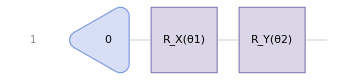

```mathematica
V=QuantumCircuitOperator[{"0","RX"[θ1]->{1},"RY"[θ2]->{1}},"Parameters"->{θ1,θ2}];
"Diagram"//V
```

Calculate ϕ (θ) from the ansatz circuit V:

```mathematica
ϕ=V[];
"Formula"//ϕ
```

(Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2])0+(-ⅈ Cos[θ2/2] Sin[θ1/2]+Cos[θ1/2] Sin[θ2/2])1

Implement the cost function ℒ as stated before:

```mathematica
ℒ[θ1_,θ2_]=ComplexExpand["Scalar"//SuperDagger[ϕ]@H@ϕ];
ℒ[θ1, θ2]//Simplify
```

Cos[θ1] (Cos[θ2]+Sin[θ2])

Calculate the ground state eigenvalue of H by minimizing 𝒻:

```mathematica
MinValue[ℒ[θ1, θ2], {θ1, θ2}]
```

-√2

### Visualizations

In order to visualize the optimization process, we need to get all the parameter values during the evolution, in this case we will use a simple gradient descent method:

```mathematica
initialPosition={0.1,0.1};
```

```mathematica
params=GradientDescent[ℒ,initialPosition];
```

It would be also useful to calculate all the cost function values during each step of the parameter evolution:

```mathematica
costs=ℒ@@@params;
```

#### Cost curve

We can visualize the evolution of our optimization during time in an Cost Curve, also known as Loss Curve:

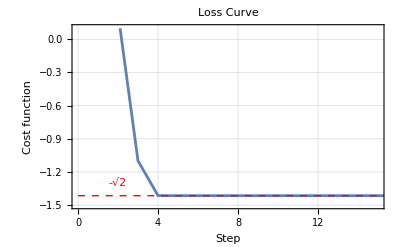

```mathematica
ListLinePlot[costs,PlotRange->{{0,15},{-1.5,0.1}},PlotLabel->"Loss Curve",Frame->True,GridLines->Automatic,FrameLabel->{"Step","Cost function"},ImageMargins->1,
Epilog->{{Red,Dashed,Line[{{0,-√2},{15,-√2}}]},{Red,Inset["-√2",{2,-1.3}]}}
]
```

#### Parameter Space

We can visualize the evolution of our optimization in the parameter space in a Contour Plot:

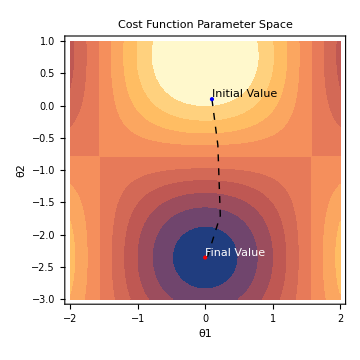

```mathematica
ContourPlot[ℒ[θ1,θ2],]
```

#### Gradient Vector Plot

The stream plot of the gradient of our cost function can provide insight into the behavior of the evolution as observed in its parameter space:

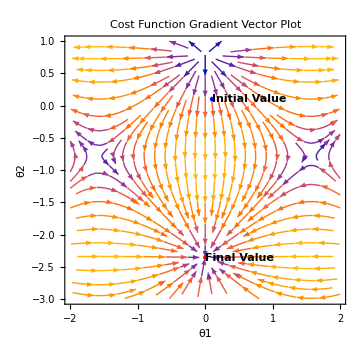

```mathematica
StreamPlot[Evaluate[-Grad[ℒ[θ1, θ2], {θ1, θ2}]],]
```

### Quantum Chemistry

The Variational Quantum Eigensolver (VQE) is a valuable tool in quantum chemistry for finding the minimal energy of a molecule. The task is essentially an optimization problem, where the goal is to minimize the total energy of the molecule with respect to the positions of the atomic nuclei.

In the case of VQE, we use parameterized quantum circuits to approximate the ground state energy of the system. This results in the determination of the minimal energy of the system, which corresponds to the lowest energy configuration of the molecule in its ground state.

This minimal energy result can be incredibly useful in determining the geometry of the molecule as well, as the lowest energy corresponds to the optimized configuration of the atomic nuclei. Therefore, although the main goal is to minimize the energy, this process can also provide insights into the stable arrangement of atoms in the molecule.

#### Toy H_2 Molecule

The current problem is finding the ground state of the H_2 molecule;,the Hamiltonian can be reduced and modeled using two qubits as:

```mathematica
H2=QuantumOperator[α("ZI"+"IZ")+β*"XX"]
```

QuantumOperator[…]

Implement the algorithm as we learned last class:

First: Parametrized quantum circuits, state and ansatz preparation.

In this case we will use a typical hardware-efficient ansatz: Two layers of Rotations and a CNOT to ensure the entanglement.

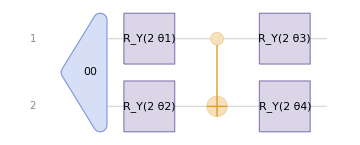

```mathematica
HEAnsatz=QuantumCircuitOperator[{"00","RY"[2 θ1]->1,"RY"[2 θ2]->2,"CNOT"->{1,2},"RY"[2 θ3]->1,"RY"[2 θ4]->2}];
HEAnsatz["Diagram"]
```

Second: Cost function ⟨ H(θ) ⟩

We need a cost function, so let’s obtain the QuantumState from the QuantumCircuit and define the bra and ket.

```mathematica
ϕ=HEAnsatz[];ϕ=SuperDagger[ϕ];
```

Finally lets compute the energy of our system and define a function that will work as the cost function. In this step we should help the optimizer by Simplifying and replacing fixed values.

```mathematica
energy=ϕ@H2@ϕ ;
```

```mathematica
values={α->0.4,β->0.2};
costH2[θ1_,θ2_,θ3_,θ4_]=FullSimplify["Scalar"//energy,{θ1,θ2,θ3,θ4}∈Reals]/.values
```

Sin[2 θ1] (0.2 Cos[2 θ3] Cos[2 θ4]-0.4 Sin[2 θ2] Sin[2 θ3])+Cos[2 θ1] (0.4 Cos[2 θ3]+Cos[2 θ4] (0.4 Cos[2 θ2]+0.2 Sin[2 θ2] Sin[2 θ3]))+(-0.4 Sin[2 θ2]+0.2 Cos[2 θ2] Sin[2 θ3]) Sin[2 θ4]

As I mentioned, the cost function we are working with is not trivial, but the advantage is that we can compute it symbolically, which significantly helps in the optimization process.

Third: Optimization

To find the optimal parameters for our quantum circuit, we can use the NMinimize function in Mathematica.

```mathematica
resultH2=NMinimize[costH2[θ1,θ2,θ3,θ4],{θ1,θ2,θ3,θ4}]
```

{-0.824621,{θ1→0.717444,θ2→-0.909051,θ3→-0.855457,θ4→2.37329}}

This function allows us to minimize the cost function by adjusting the parameters, and after performing this minimization, we obtain the optimized parameters and the minimum value of the cost function, which in this case is approximately -0.824.

```mathematica
paramH2=Last[resultH2]//Association
```

<|θ1→0.717444,θ2→-0.909051,θ3→-0.855457,θ4→2.37329|>

Now that we have the optimal value, it is insightful to inspect the behavior of the cost function around these points. Since we have four variables (the parameters in the ansatz), we need to fix two of the values in order to visualize the function.

We can do this by using a ContourPlot, which will allow us to observe the shape of the cost function in two dimensions.

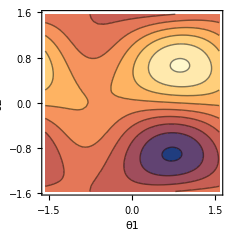

```mathematica
ContourPlot[costH2[θ1,θ2,paramH2[θ3],paramH2[θ4]],{θ1,-π/2,π/2},{θ2,-π/2,π/2},FrameLabel->Automatic]
```

ContourPlot is useful here because it highlights where the cost function attains higher and lower values. In this plot, the lighter sections correspond to higher values, and the blue sections represent the lowest values of the cost function.

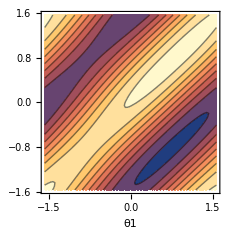

```mathematica
ContourPlot[costH2[θ1,paramH2[θ2],θ3,paramH2[θ4]],{θ1,-π/2,π/2},{θ3,-π/2,π/2},FrameLabel->Automatic]
```

If the optimization algorithm has started with a point near the blue section (where the minimum lies), we can expect it to converge towards this blue region, as this represents the optimal set of parameters. The algorithm searches for regions where the cost is minimized, and this plot helps visualize the “shape” of the function.

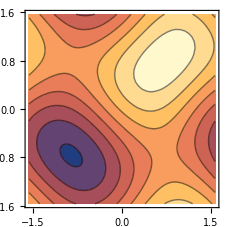

```mathematica
ContourPlot[costH2[paramH2[θ1],paramH2[θ2],θ3,θ4],{θ3,-π/2,π/2},{θ4,-π/2,π/2}]
```

When the cost function is relatively simple and can be expressed symbolically, the ContourPlot can exhibit repetitive patterns. This repetition often results from the periodic nature of trigonometric functions (e.g., sin⁡and cos) that may appear in the cost function due to the rotation gates used in the ansatz.

Example from  https://arxiv.org/pdf/1909.05074v1

#### Trihydrogen cation

In this example we will obtain the minimal energy for the molecule Cation H_3^+.

First we will use some python code from PennyLane to obtain the Hamiltonian corresponding to the H3 cation.

We just need to indicate the molecules “H” and the coordinates:

import pennylane as qml
from pennylane import numpy as np

symbols = ["H", "H", "H"]
coordinates = np.array([0.028, 0.054, 0.0, 0.986, 1.610, 0.0, 1.855, 0.002, 0.0])

# Building the molecular hamiltonian for the trihydrogen cation
hamiltonian, qubits = qml.qchem.molecular_hamiltonian(symbols, coordinates, charge=1)

qml.matrix(hamiltonian)

NumericArray[…]

In case Python is not available, you can import it from this location:

```mathematica
Import["https://wolfr.am/1uXbew3vg"]
```

NumericArray[…]

Finally we obtain a NumericArray which we will turn into a QuantumOperator:

```mathematica
H3=QuantumOperator[%//Normal]
```

QuantumOperator[…]

If we have no prior knowledge of the structure of the circuit, a reasonable starting point could be a layered circuit consisting of rotations around the Y-axis and CNOT gates.

To encode the occupation numbers of the molecular spin-orbitals, we would need six qubits.

```mathematica
param=GenerateParameters[6,2];
basicMixAnsatz=QuantumCircuitOperator[{
ParametrizedLayer["RY",Range[1,6]],
EntanglementLayer["CNOT",Range[6]],
"Barrier",
ParametrizedLayer["RY",Range[7,12]]
},
"Parameters"->param
];
```

If you’d like to learn how to construct layered circuits using ParametrizedLayer and EntanglementLayer please refer to the Quantum Optimization documentation.

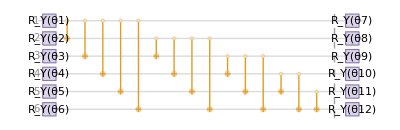

```mathematica
basicMixAnsatz["Diagram",ImageSize->Full]
```

In this case, you can expect a very complex symbolic cost function. To handle this, we could choose to implement a numerical function instead.

```mathematica
stateAnsatz=basicMixAnsatz[];
```

```mathematica
matrixH3=H3["Matrix"];
```

We begin by using Module to define the quantum state with parameters replaced by real numbers.  Next, we define the ket and bra, and then compute the scalar resulting from the expectation value of the Hamiltonian H.

```mathematica
ClearAll[meanEnergy]
meanEnergy[values_,H_]:=Module[{ket,bra,state},
state=stateAnsatz[AssociationThread[param,values]];
ket=state["StateVector"];
bra=SuperDagger[state]["StateVector"];
Re[bra.H.ket]
]
```

After defining the cost function, we can apply a classical optimizer starting from an initial guess to find the minimum energy value.

```mathematica
init=Thread[{param,{π,0,0,0,π/2,π,0,0,0,0,π,0}}];
```

```mathematica
FindMinimum[meanEnergy[param,matrixH3],init]//Quiet
```

{-1.30949,{θ1→3.13598,θ2→-0.196715,θ3→-0.00696906,θ4→-0.00209702,θ5→1.45483,θ6→3.14184,θ7→-3.02125×10^-7,θ8→-2.94889×10^-7,θ9→2.37779×10^-7,θ10→-8.8975×10^-7,θ11→3.14373,θ12→-3.14374}}

If we are interested in obtaining the geometry of the system, we would need to introduce a parameterized Hamiltonian for optimization as well, to optimize both the energy and the geometry.